```mathematica
NewList={}
```

{}

```mathematica
newItem[text_,do_]:=AppendTo[NewList,{text, do}]
```

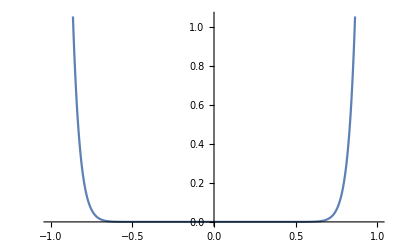
{{
 Half Baby Carrot (y==20 x^20),-Graphics-}}

```mathematica
newItem[Style["Half Baby Carrot""\n"TraditionalForm[y==20*x^20],FontSize->20],Plot[20*(x)^20,{x,-1,1}]]
```

```mathematica
graphic1 = Rasterize[GraphicsGrid[NewList,Frame->True,Spacings->Automatic,ImageSize->{800,325}]]
```

-Graphics-

```mathematica
Export["/home/nathan/QEA-Homework/homework/hw1/part13.png",graphic1,"PNG"]
```

/home/nathan/QEA-Homework/homework/hw1/part13.png